```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
ClearAll[ eqn,sol,α,kappa,T0,Lx, Ly, Lz, Z0,x,y,z,yTube,rTube, rBeam,beamTube,topTube, bottomTube, copperRectangularRegion,copperRegionWithBeam,copperRegionIncomplete,copperRegionComplete,copperMeshRegion,powerDensity3D,powerDensityFun3D,cpsInterFunc, A, s]
```

```mathematica
cpsInterFunc=Import["/home/hovanes/Documents/Wolfram\ Mathematica/cps_vitaly_core_fine.m"]
```

InterpolatingFunction[{{-2.175, 2.175}, {-13.475, 13.475}, {78.1, 130.9}}, <>]

```mathematica
powerDensity3D[x_,y_,z_]=Piecewise[{{cpsInterFunc[x,y,z],-2.175≤x<=2.175&&-13.475≤y<=13.475&&78.1≤z<=130.9}},0]
```

Piecewise[{{InterpolatingFunction[{{-2.175, 2.175}, {-13.475, 13.475}, {78.1, 130.9}}, <>][x,y,z], -2.175≤x≤2.175&&-13.475≤y≤13.475&&78.1≤z≤130.9}, {0, True}}]

```mathematica
α=0.0005;kappa=0.00385;T0=40;
Lx=4.4;Ly=27;Lz=53;Z0=104.5; (*Lz=10; Z0=95;*)
yTube=9.5; rTube=1.5; rBeam=0.3175;
A=1.0;s=0.5;
```

```mathematica
(*powerDensity3D[x_,y_,z_]=A*Exp[-((x-0)^2/(2 s^2)+(y-0)^2/(2(2*s)^2)+(z-Z0)^2/(2(4*s)^2))];*)
```

```mathematica
(*NIntegrate[y*powerDensity3D[x,y,z],{x,-5*Pi/3,Pi/3},{y,0,ymax},{z,0,L},WorkingPrecision->9]*)
```

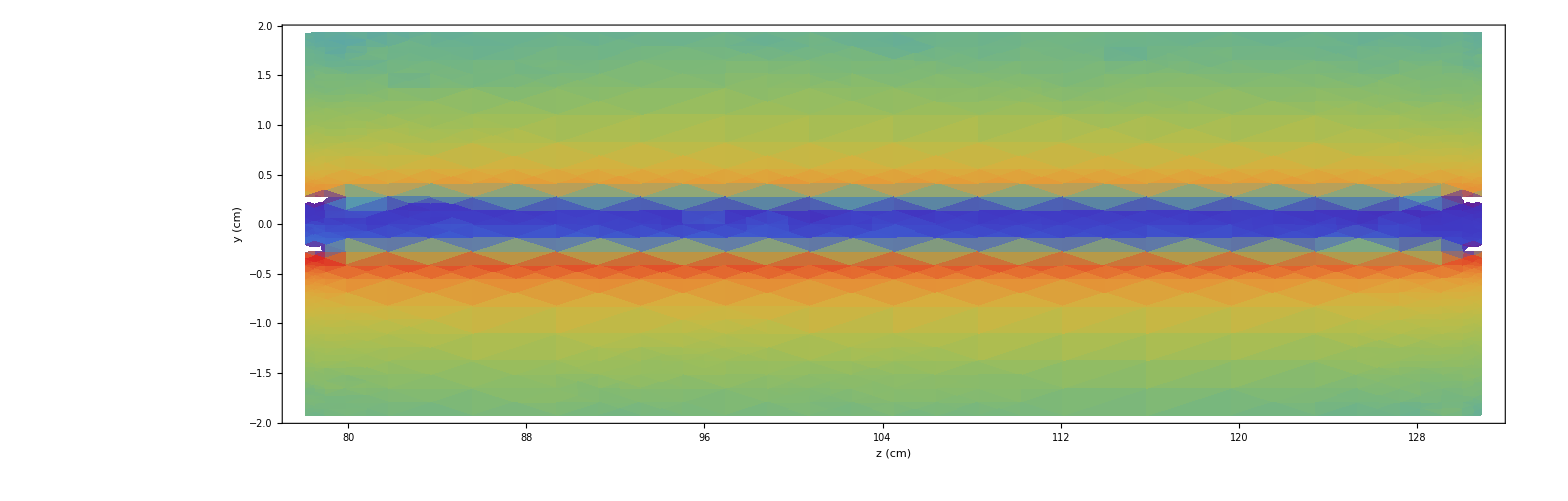

```mathematica
DensityPlot[powerDensity3D[0,y,z],{z,Z0-Lz/2,Z0+Lz/2},{y,-Ly/14,Ly/14},ColorFunction->{"Rainbow"},PlotRange->Automatic,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{1600,600},FrameLabel->{"z (cm)", "y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->0.32]
```

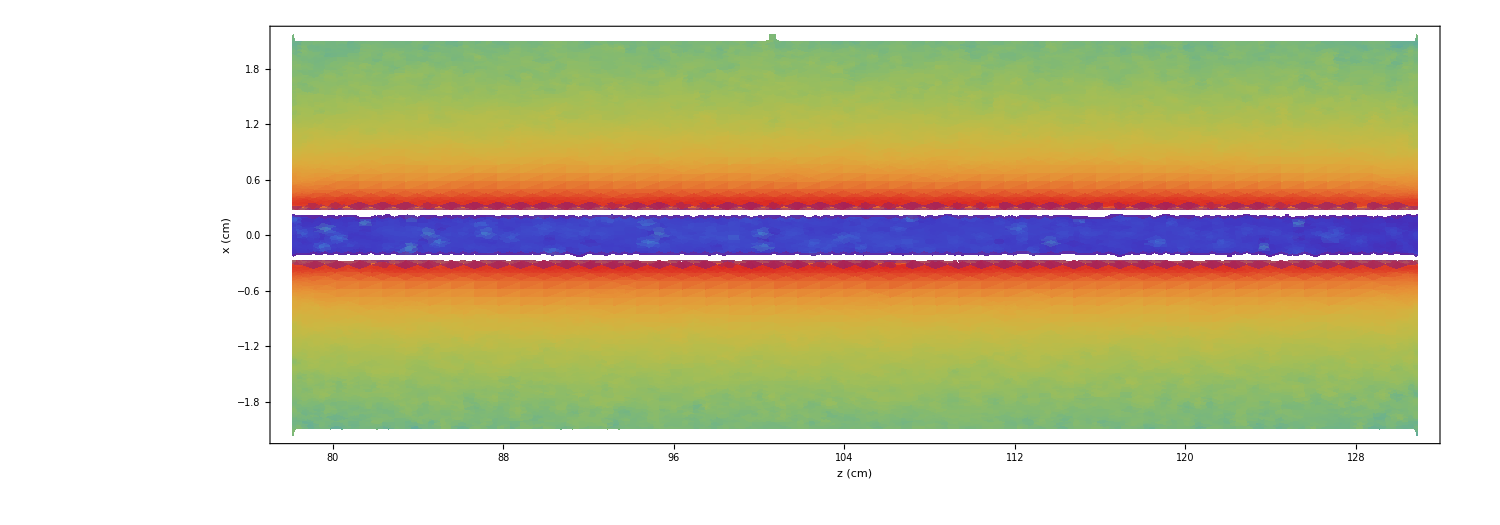

```mathematica
DensityPlot[powerDensity3D[x,0,z],{z,Z0-Lz/2,Z0+Lz/2},{x,-Lx/2,Lx/2},ColorFunction->{"Rainbow"},PlotRange->Automatic,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{1500,600},FrameLabel->{"z (cm)", "x (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},PlotPoints->50,AspectRatio->0.35]
```

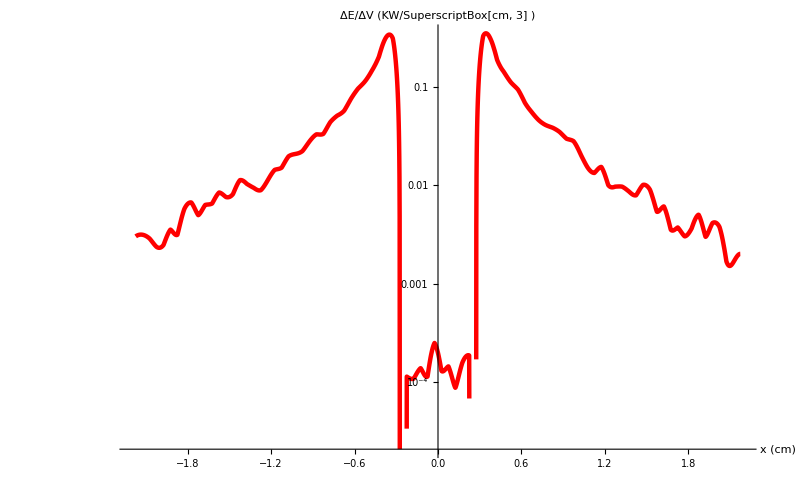

```mathematica
LogPlot[powerDensity3D[x,0,Z0],{x,-Lx/2,Lx/2},AxesLabel->{"x (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

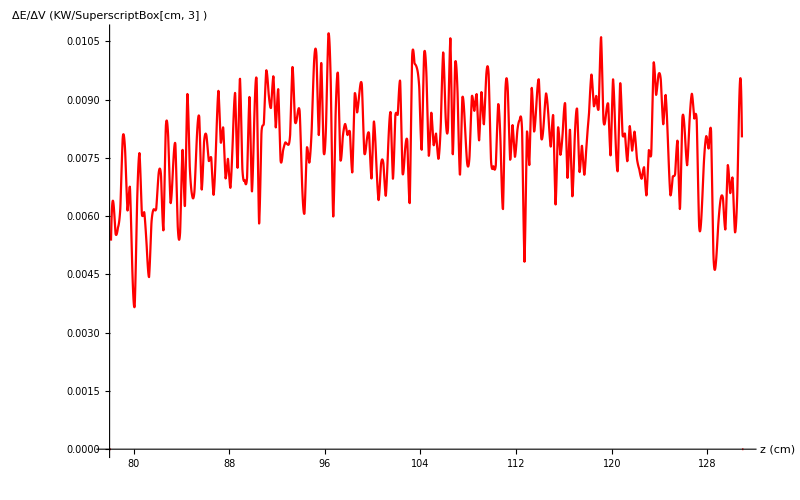

```mathematica
Plot[powerDensity3D[1.0,1.0,z],{z,Z0-Lz/2,Z0+Lz/2}, AxesLabel->{"z (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

```mathematica
DensityPlot[powerDensity3D[x,y,99],{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},ColorFunction->"Rainbow",PlotRange->Automatic,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{400,1200},FrameLabel->{"x (cm)", "y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{22,GrayLevel[0],Italic},PlotPoints->50,AspectRatio->4]
```

-Graphics-

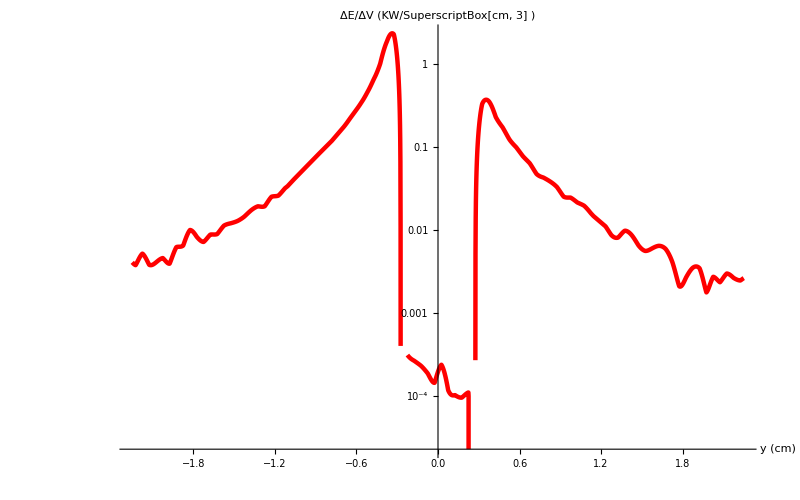

```mathematica
LogPlot[powerDensity3D[0,y,Z0],{y,-Ly/12,Ly/12},AxesLabel->{"y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

```mathematica
copperRectangularRegion=Cuboid[{-Lx/2,-Ly/2,Z0-Lz/2},{Lx/2,Ly/2,Z0+Lz/2}];
```

```mathematica
beamTube=Cylinder[{{0,0,Z0-Lz/2},{0,0,Z0+Lz/2}},rBeam];
```

```mathematica
topTube=Cylinder[{{0,yTube,Z0-Lz/2},{0,yTube,Z0+Lz/2}},rTube];
```

```mathematica
bottomTube=Cylinder[{{0,-yTube,Z0-Lz/2},{0,-yTube,Z0+Lz/2}},rTube];
```

```mathematica
(*tubesRegions = BooleanRegion[Or,{beamTube,topTube,bottomTube}]*)
```

```mathematica
(*copperRegionComplete=BooleanRegion[Xor,{copperRectangularRegion,bottomTube}]*)
```

```mathematica
(*RegionPlot3D[tubesRegions,PerformanceGoal->"Quality",Mesh->All]*)
```

```mathematica
(*RegionPlot3D[copperRegionComplete,PerformanceGoal->"Quality",Mesh->All]*)
```

```mathematica
copperRegionComplete=RegionDifference[copperRectangularRegion,RegionUnion[RegionUnion[topTube,bottomTube],beamTube]];
```

```mathematica
(*RegionPlot3D[copperRegionComplete]*)
```

```mathematica
(*copperBoundaryMesh=ToBoundaryMesh[copperRegionComplete,MaxBoundaryCellMeasure->{"Length"->0.03}];*)
```

```mathematica
(*copperBoundaryMesh["Wireframe"]*)
```

```mathematica
copperMeshRegion=ToElementMesh[copperRegionComplete,MeshQualityGoal->"Maximal",MaxBoundaryCellMeasure->{"Length"->0.05},MaxCellMeasure->{"Length"->0.3}];
```

```mathematica
(*RegionPlot3D[copperMeshRegion,AxesLabel->Automatic,PerformanceGoal->"Speed",Mesh->None]*)
```

```mathematica
(*copperMeshRegion["Wireframe"]*)
```

```mathematica
eqn=-Laplacian[u[x,y,z],{y,x,z}]==1/kappa*powerDensity3D[x,y,z]+NeumannValue[0.0,{x,y,z}∈RegionBoundary@ copperRectangularRegion] +NeumannValue[0.0,{x,y,z}∈RegionBoundary@ beamTube] +NeumannValue[-α/kappa*(u[x,y,z]-T0), {x,y,z}∈RegionBoundary@topTube] + NeumannValue[-α/kappa*(u[x,y,z]-T0), {x,y,z}∈RegionBoundary@bottomTube];
```

```mathematica
(*sol=NDSolveValue[{eqn,DirichletCondition[ u[x,y,z]==T0, {x,y,z}∈RegionBoundary@topTube] , DirichletCondition[ u[x,y,z]==T0, {x,y,z}∈RegionBoundary@bottomTube ]  }, u,{x, y,z} ∈ copperMeshRegion];*)
```

```mathematica
sol=NDSolveValue[eqn , u,{x, y,z} ∈ copperMeshRegion];
```

```mathematica
(*sol=Import["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/Results4VitalysModel/tSolutionFunc_100degT0_goodResults.m"]*)
```

```mathematica
(*Export["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/t_distribution_3D_VitalyReference_boundaryTdrop.m", sol]*)
```

/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_distribution_3D_VitalyReference_boundaryTdrop.m

```mathematica
DensityPlot[sol[x,y,97], {x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,300},ImageSize->{500,1600},FrameLabel->{"x (cm)", "y (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},PlotPoints->150,AspectRatio->6]
```

-Graphics-

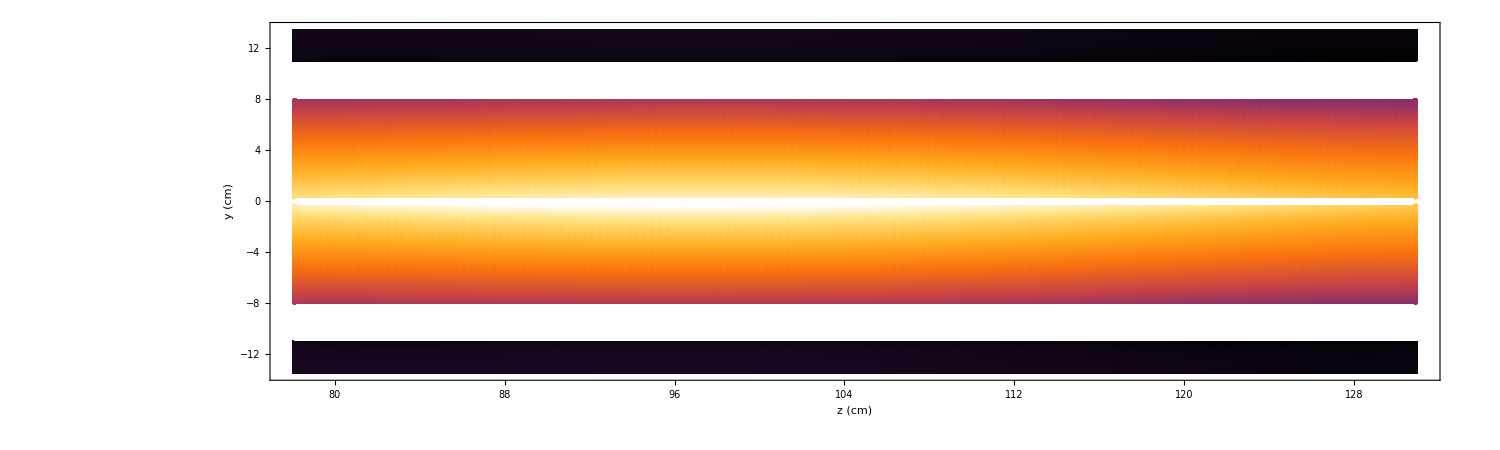

```mathematica
DensityPlot[sol[0,y,z], {z,Z0-Lz/2,Z0+Lz/2},{y,-Ly/2,Ly/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{1500,500},FrameLabel->{ "z (cm)", "y (cm)","T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},PlotPoints->150,AspectRatio->0.3]
```

```mathematica
DensityPlot[sol[x,-0.35,z],{z,Z0-Lz/2,Z0+Lz/2},{x,-Lx/2,Lx/2} ,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->Full,ImageSize->{1500,500},FrameLabel->{ "z (cm)", "x (cm)","T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},PlotPoints->150,AspectRatio->0.3]
```

-Graphics-

```mathematica
SliceContourPlot3D[sol[x,y,z], "CenterPlanes",{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,Z0-Lz/2,Z0+Lz/2}, PlotTheme->"Detailed", ImageSize->{800,800},PlotLabel->"T (^oC)",AxesLabel->{ "x (cm)", "y (cm)","z (cm)"},LabelStyle->{22,GrayLevel[0],Italic}]
```

-Graphics3D-

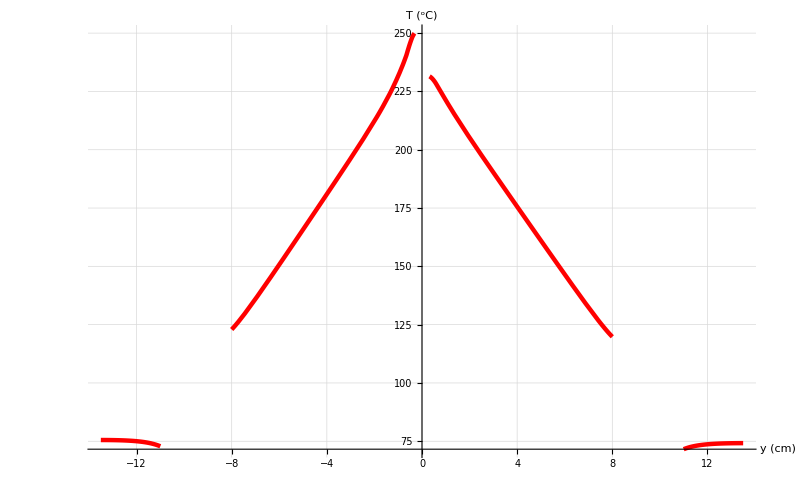

```mathematica
Plot[sol[0,y,97], {y,-Ly/2,Ly/2},GridLines->Automatic,PlotRange->Full,AxesLabel->{"y (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

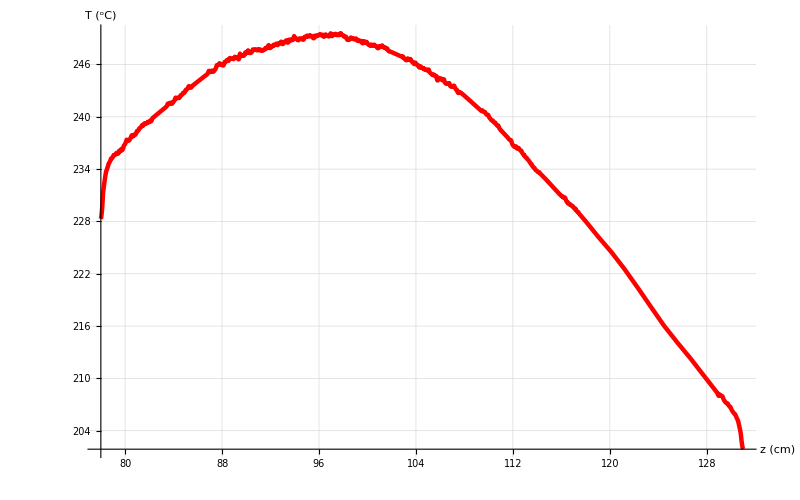

```mathematica
Plot[sol[0,-0.35,z], {z,Z0-Lz/2,Z0+Lz/2},GridLines->Automatic,PlotRange->Full,AxesLabel->{"z (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

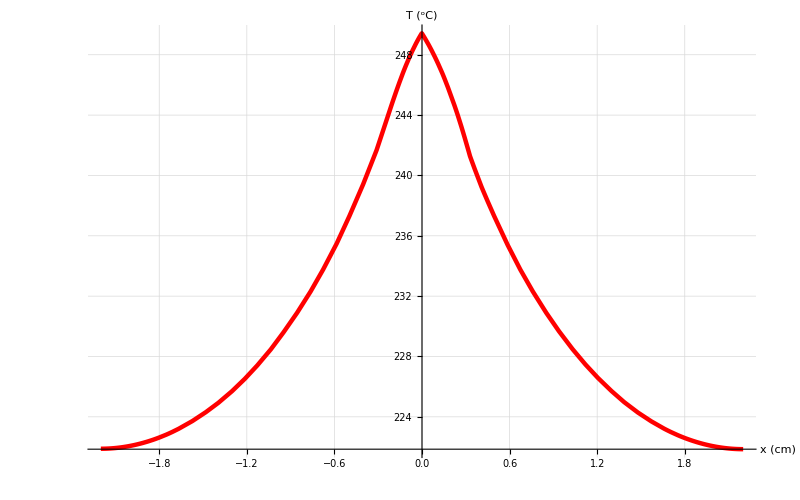

```mathematica
Plot[sol[x,-0.35,97], {x,-Lx/2,Lx/2},GridLines->Automatic,PlotRange->Full,AxesLabel->{"x (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```